## Chapter 2: Multiple Buildings and Complex Campuses

### Overview

## Data Models

There are three primary concepts that this application models.  Those are Campus Buildings, Points of Delivery, and Measured Quantities.

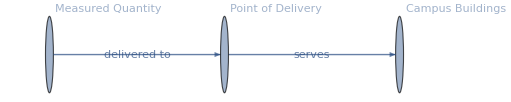

```mathematica
importUserFunctionalGraph=Graph[{
Labeled["Point of Delivery"->"Campus Buildings","serves"],
Labeled["Measured Quantity"->"Point of Delivery","delivered to"]},
VertexLabels->"Name",EdgeLabels->True]
```

#### Campus Buildings

Campus Buildings will often have their own points of delivery for each commodity consumed, however on many campuses it is common for many buildings to share points of delivery, for example where an electric utility places a meter on a transformer that provides power to multiple buildings.

#### Points of Delivery

Points of Delivery, sometimes referred to Service Delivery Points, or Service Point Locations are the point at which a commodity is delivered from the  supplier to the  customer.  In the case of electricity supply, the Point of Delivery is typically the point at which the utility places a meter that measures electrical consumption by the customer.  In the case of fuel oil deliveries it would be the fill tube of the customer’s fuel tank.  In this case the measurement of the quantity delivered is done by a meter on the fuel oil truck, not by a meter installed at the customer’s facility.  Points of Delivery often supply a single building with an  commodity, although in many instances a point of delivery may supply many buildings, such as delivery of wood chips to a biomass boiler that heats many buildings on campus.  In some cases a Point of Delivery may not have any association with a building, such as metered street lights or water pumps.  It is for these reasons of multiple buildings being served by a single service delivery point, or a service delivery point having no building at all, that we require a concept distinct from campus buildings to associate measured quantities to.

#### Measured Quantities

There are a few flavors of measured quantities whose differences arise from different delivery and metering technologies.  In most cases a single quantity will be associated to a Point of Delivery, however electrical meters often measure multiple distinct units of measure, and often in two directions when a generator is installed behind the meter so that electricity is at times

## Entering Master Data

```mathematica
TextSentences[WikipediaData["master data"]][[;;5]]
```

{Master data represents the business objects that contain the most valuable, agreed upon information shared across an organization.,It can cover relatively static reference data, transactional, unstructured, analytical, hierarchical and metadata.,It is the primary focus of the information technology (IT) discipline of master data management (MDM).,Master data is usually non-transactional in nature, but in some cases gray areas exist where transactional processes and operations may be considered master data by an organization.,For example, master data may contain information about customers, products, employees, materials, suppliers, and vendors.}

Buildings and Points of Delivery are the  master data objects of interest to a campus energy management project.  By collecting and maintaining accurate master data you will be able to perform analyses that go far beyond what is possible with collecting energy consumption data alone.  For instance, if you have access to accurate information regarding the floor area of each building on campus, you will be able to calculate the energy intensity of each building.  If you include each building’s function, such as athletic facility, dormitory, administrative building you will be able to determine how much each function contributes to your school’s energy consumption.  
There are several possible methods of building a master data repository with the Wolfram Language.  This project is using the language’s EntityStore functionality.  If you wish, one can enter master data by brute force, and fully compose the code for each entry.  It is also possible to use the Language’s form building capabilities to construct a form to facilitate data entry.